```mathematica
file=Import["D:\\VisualStdudio\\calculatem\\calculation-methods-labs\\lab_iter_methods\\lab_iter_methods\\WoframOmegaVsIteration.txt","Table"];
```

```mathematica
step = Length[file[[1]]];
sizeofmas=2;
```

```mathematica
omega = file[[1]];
```

```mathematica
iter1= Table[file[[i]],{i,2,sizeofmas+1}]; (*Stopcriteria One*)
```

```mathematica
iter2 =  Table[file[[i]],{i,sizeofmas+2,2*sizeofmas+1}];(*Stopcriteria Two*)
```

```mathematica
iter3 = Table[file[[i]],{i,2*sizeofmas+2,3*sizeofmas+1}];(*Stopcriteria third*)
```

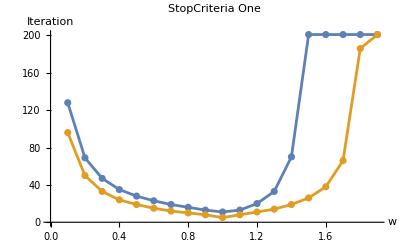

```mathematica
Show[ListLinePlot[Table[Table[{omega[[j]], iter1[[i]][[j]]},{j,1,step}] ,{i,1,sizeofmas}],AxesLabel->{"w", "Iteration"}, LabelStyle->Directive[Blue, Bold],PlotLabel->"StopCriteria One"],ListPlot[Table[Table[{omega[[j]], iter1[[i]][[j]]},{j,1,step}] ,{i,1,sizeofmas}]] ]
```

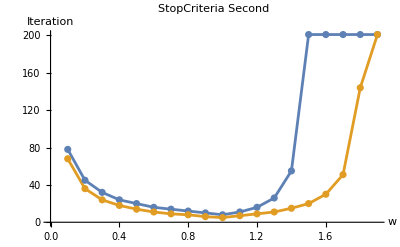

```mathematica
Show[ListLinePlot[Table[Table[{omega[[j]], iter2[[i]][[j]]},{j,1,step}] ,{i,1,sizeofmas}],AxesLabel->{"w", "Iteration"}, LabelStyle->Directive[Blue, Bold],PlotLabel->"StopCriteria Second"],ListPlot[Table[Table[{omega[[j]], iter2[[i]][[j]]},{j,1,step}] ,{i,1,sizeofmas}]] ]
```

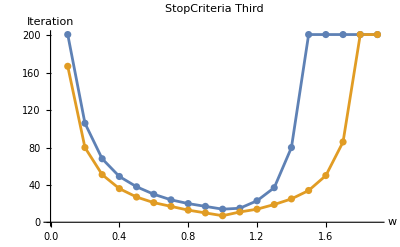

```mathematica
Show[ListLinePlot[Table[Table[{omega[[j]], iter3[[i]][[j]]},{j,1,step}] ,{i,1,sizeofmas}],AxesLabel->{"w", "Iteration"}, LabelStyle->Directive[Blue, Bold],PlotLabel->"StopCriteria Third"],ListPlot[Table[Table[{omega[[j]], iter3[[i]][[j]]},{j,1,step}] ,{i,1,sizeofmas}]] ]
```